See CVI Gaussian Optics notes, eq 2.20 through 2.23

```mathematica
Clear["Global`*"]
```

```mathematica
nm=10^-9;
μm=10^-6;
```

```mathematica
λtrap=700;
T0=(1.5*120/25)/18; (*using 1/e^2 diameters*)
NA0=0.55;
```

```mathematica
K[T_]:=1.6449+0.6460/(T-0.2816)^1.821-0.5320/(T-0.2816)^1.891;
d[T_,λ_,NA_]:=K[T] λ /(2 NA);
```

Trap diameter (1/e^2) :
equivalent to 2x w0 (w0=beam waist)

```mathematica
d[T0,λtrap nm,NA0]/nm
```

1923.62

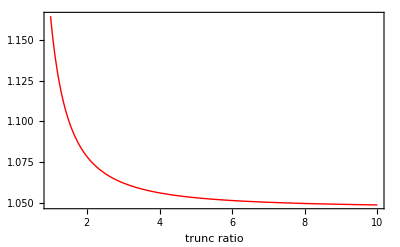

```mathematica
Plot[d[T,λtrap nm,NA0]/μm,{T,1,10},PlotRange->All,Axes->False,Frame->True,FrameLabel->{"trunc ratio"}]
```

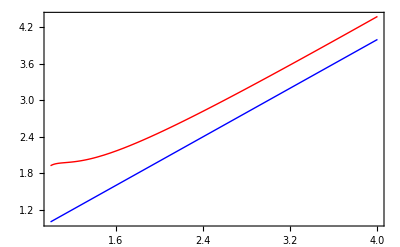

```mathematica
Plot[{d[T0*b,λtrap nm,NA0/b]/μm,b},{b,1,4},PlotRange->All]
```

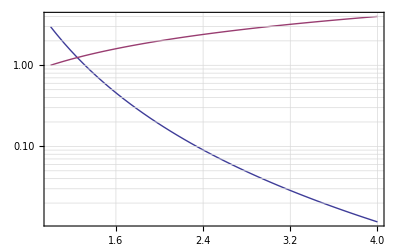

```mathematica
LogPlot[{3*Aperture^-4,1*Aperture},{Aperture,1,4},GridLines->Automatic]
```

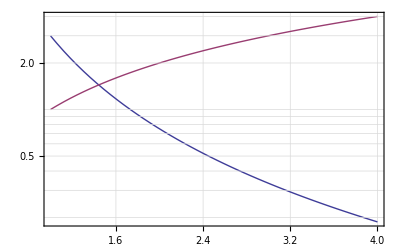

```mathematica
LogPlot[{3*Aperture^-2,1*Aperture},{Aperture,1,4},GridLines->Automatic]
```